#### Define fields, metric, potential, parameters

```mathematica
nf=2;
f=Table[Symbol["f"<>ToString[i]][t],{i,nf}];
{σ,θ}=f;
(*fields={σ,χ,θ};*)

df=Table[Symbol["f"<>ToString[i]]'[t],{i,nf}](*f[[#]]'[t]&/@Table[n,{n,1,nf}]*);
ddf=Table[Symbol["f"<>ToString[i]]''[t],{i,nf}];

G=({{1, 0}, {0, (1+ξ σ)^2}});
Ginv=Inverse[G];

dfNorm2=Simplify[df.G.df];
dfNorm=Simplify@Sqrt[dfNorm2];
sig=df/dfNorm;
K=1/2 dfNorm2;

gBCH=1+ξ σ;
V=Λ(1-Subscript[C, 2] θ^2+Subscript[C, 1](1-Exp[-σ^2/Σ^2]));
(*Vfn[σ_,θ_]:=Λ(1-Subscript[C, 2] θ^2+Subscript[C, 1](1-Exp[-σ^2/Σ^2]));*)
```

```mathematica
Vgrad=Grad[V,f];
VgradUp=Ginv.Vgrad;
Vhess=D[V,{f,2}];
Vsig=sig.Vgrad;

H=Sqrt[(K+V)/3];
eH=K/H^2;
```

```mathematica
(*Vgrad/.{V->vBCH}*)
```

```mathematica
(*VgradUp/.{g->gBCH,V->vBCH}*)
```

#### Geometric objects and mass matrix

```mathematica
csymb:=Simplify@Table[1/2 Sum[Ginv[[i,m]](D[G[[m,k]],f[[j]]]+D[G[[j,m]],f[[k]]]-D[G[[j,k]],f[[m]]]),{m,nf}],{i,nf},{j,nf},{k,nf}];
riemann:=Simplify@Table[D[csymb[[i,j,k]],f[[l]]]-D[csymb[[i,j,l]],f[[k]]]+Sum[csymb[[m,j,k]]csymb[[i,l,m]],{m,nf}]-Sum[csymb[[m,j,l]]csymb[[i,k,m]],{m,nf}],{i,nf},{j,nf},{l,nf},{k,nf}];
ricciT:=Table[Sum[riemann[[i,j,i,k]],{i,nf}],{j,nf},{k,nf}];
ricciS:=Sum[(Ginv.ricciT)[[i,i]],{i,nf}];
```

```mathematica
csymb//MatrixForm
(*ricciS*)
```

((0
0) | (0
-ξ (1+ξ f1[t]))
(0
ξ/(1+ξ f1[t])) | (ξ/(1+ξ f1[t])
0))

```mathematica
ricciS
```

0

```mathematica
Ddf=ddf+Table[Sum[csymb[[i,j,k]]df[[j]]df[[k]],{j,nf},{k,nf}],{i,nf}];
wVec=D[sig,t]+Table[Sum[csymb[[i,j,k]]df[[j]]sig[[k]],{j,nf},{k,nf}],{i,nf}];
w2=wVec.G.wVec;
w=Simplify@Sqrt[w2];
s=Simplify[wVec/w];
```

```mathematica
DdV=Vhess-Table[Sum[csymb[[i,j,k]]Vgrad[[i]],{i,nf}],{j,nf},{k,nf}];
massMx=Ginv.DdV-Table[Sum[riemann[[i,l,m,j]]df[[l]]df[[m]],{l,nf},{m,nf}],{i,nf},{j,nf}];
mSigSig=sig.G.massMx.sig;
mss=s.G.massMx.s;
```

```mathematica
eom=Simplify[Ddf+3H df+VgradUp];
(*eomBCH =Simplify[ eom/.{V->vBCH}];*)
```

```mathematica
eom//MatrixForm
(*eomBCH//MatrixForm*)
```

((2 ⅇ^(-f1[t]^2/Σ^2) Λ f1[t] C_1)/Σ^2-ξ (1+ξ f1[t]) f2'[t]^2+√(3/2) f1'[t] √(2 Λ (1+(1-ⅇ^(-f1[t]^2/Σ^2)) C_1-f2[t]^2 C_2)+f1'[t]^2+(1+ξ f1[t])^2 f2'[t]^2)+f1''[t]
-(2 Λ f2[t] C_2)/(1+ξ f1[t])^2+(2 ξ f1'[t] f2'[t])/(1+ξ f1[t])+√(3/2) f2'[t] √(2 Λ (1+(1-ⅇ^(-f1[t]^2/Σ^2)) C_1-f2[t]^2 C_2)+f1'[t]^2+(1+ξ f1[t])^2 f2'[t]^2)+f2''[t])

#### Solve background equations of motion

```mathematica
Λval=3.99*^-13;
Σval=0.775;
ξval=3.32/Σval;
C1val=10;
C2val=0.0476;
(*C3val=1;*)
σi=2.12;
θi=9.84*^-3;
```

```mathematica
Plot3D[Vfn[σ,θ]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval},{σ,-1,3},{θ,-2,2}]
(*Plot3D[vEGNO[x1,y1]//.{a->aVal,c->cVal,m->1},{x1,0.4,0.6},{y1,0,3}]*)
```

-Graphics3D-

```mathematica
tEnd=1*^8;
soln=NDSolve[{Evaluate[eom[[1]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}]==0,Evaluate[eom[[2]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}]==0,f1[0]==σi,f2[0]==θi,f1'[0]==0,f2'[0]==0},{f1,f2},{t,0,tEnd}(*,MaxSteps->Infinity,WorkingPrecision->30,InterpolationOrder->All*)]
```

{{f1→InterpolatingFunction[…],f2→InterpolatingFunction[…]}}

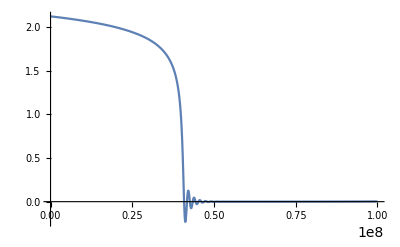

```mathematica
Plot[Evaluate[f1[t]/.soln],{t,0,tEnd}]
```

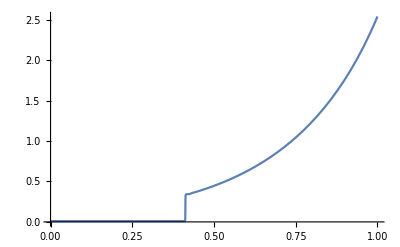

```mathematica
Plot[Evaluate[f2[t]/.soln],{t,0,tEnd}]
```

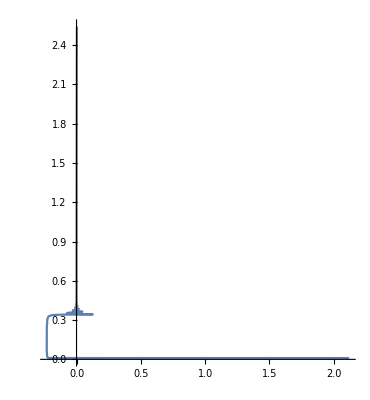

```mathematica
ParametricPlot[Evaluate[{σ,θ}/.soln],{t,0,tEnd},AspectRatio->Full]
```

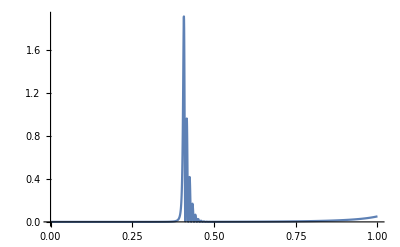

```mathematica
Plot[Evaluate[eH//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln],{t,0,tEnd},PlotRange->All]
```

```mathematica
infEnd=FindRoot[Evaluate[eH//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln]-1,{t,tEnd*0.8}]
```

InterpolatingFunction::dmval: Input value {4259.17} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {t} = {18484.6}.

{t→1679.51}

```mathematica
Ninf=NIntegrate[Evaluate[H//.{g->gEGNO,V->vEGNO,a->0.5,c->1000,m->1}/.soln],{t,0,t/.infEnd}]
```

{1066.36}

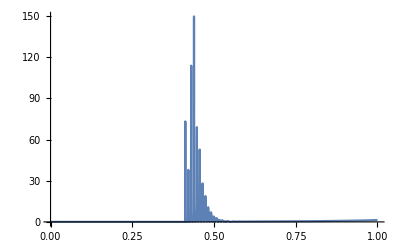

```mathematica
Plot[Evaluate[w/H//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln],{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

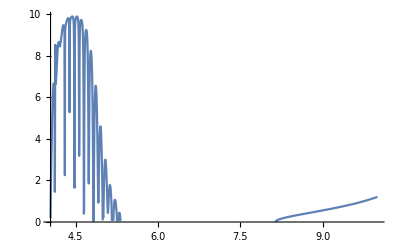

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

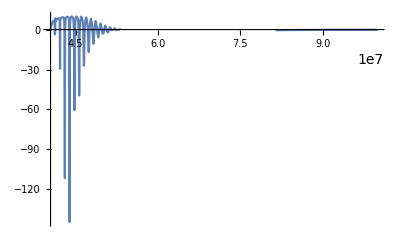

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]-w/H]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

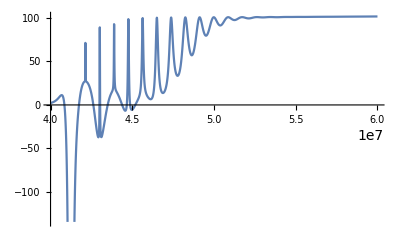

```mathematica
Plot[Evaluate[mss/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln,{t,tEnd*0.4,tEnd*0.6(*t/.infEnd*)},PlotRange->Automatic]
```

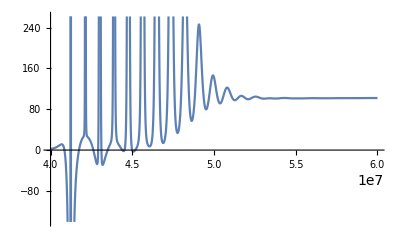

```mathematica
Plot[Evaluate[(mss+3 w^2)/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln,{t,tEnd*0.4,tEnd*0.6(*t/.infEnd*)},PlotRange->Automatic]
```

```mathematica
Plot[Evaluate[f1[t]/.soln],{t,0,tEnd}]
```

-Graphics-

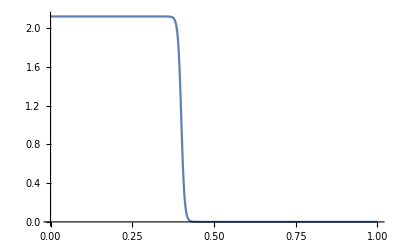

```mathematica
Plot[σi(1-Tanh[(t-tEnd*0.4)/(tEnd*0.01)])/2,{t,0,tEnd},PlotRange->All]
```

```mathematica
Plot[Evaluate[f2[t]/.soln],{t,0,tEnd}]
```

-Graphics-

```mathematica
tEnd=1*^8;
```

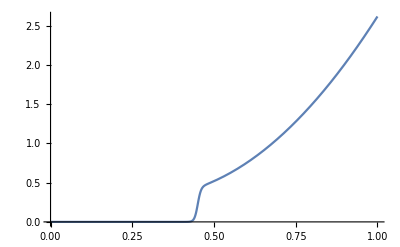

```mathematica
Plot[(1+Tanh[(t-tEnd*0.45)/(tEnd*0.01)])/2*1/3(14((t-tEnd*0.3)/tEnd)^2+1),{t,0,tEnd},PlotRange->All]
```

```mathematica
ParametricPlot[Evaluate[{σ,θ}/.soln],{t,0,tEnd},AspectRatio->Full]
```

-Graphics-

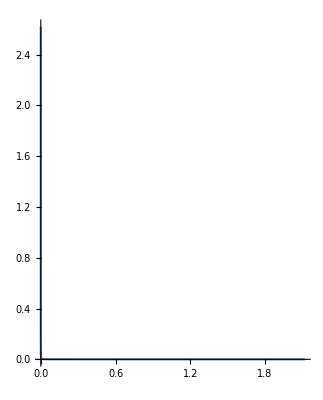

```mathematica
ParametricPlot[{σi(1-Tanh[(t-tEnd*0.4)/(tEnd*0.01)])/2,(1+Tanh[(t-tEnd*0.45)/(tEnd*0.01)])/2*1/3(14((t-tEnd*0.3)/tEnd)^2+1)},{t,0,tEnd},AspectRatio->Full]
```

```mathematica
σFake=σi(1-Tanh[(t-tEndTemp*0.4)/(tEndTemp*0.01)])/2;
θFake=(1+Tanh[(t-tEndTemp*0.45)/(tEndTemp*0.01)])/2*1/3(14((t-tEndTemp*0.3)/tEndTemp)^2+1);
σdFake=D[σFake,t];
θdFake=D[θFake,t];
velFake={σdFake,θdFake};
```

```mathematica
FullSimplify@θdFake
```

1/(3 tEndTemp^3)(700. (t^2-0.6 t tEndTemp+0.161429 tEndTemp^2) Sech[45.-(100. t)/tEndTemp]^2+14 (t-0.3 tEndTemp) tEndTemp (1+Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))

```mathematica
Gfake=G/.{σ->σFake,ξ->ξval};
sigFake=Simplify[velFake/Sqrt[velFake.Gfake.velFake]];
```

```mathematica
Simplify@sigFake
```

{-((1. Sech[40.-(100. t)/tEndTemp]^2)/(tEndTemp √(1/tEndTemp^6(1. tEndTemp^4 Sech[40.-(100. t)/tEndTemp]^4+0.00193821 (50. (t^2-0.6 t tEndTemp+0.161429 tEndTemp^2) Sech[45.-(100. t)/tEndTemp]^2+(t-0.3 tEndTemp) tEndTemp (1+Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))^2 (5.5409-4.5409 Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)))),((2.20126 t^2-1.32075 t tEndTemp+0.355346 tEndTemp^2) Sech[45.-(100. t)/tEndTemp]^2+tEndTemp (0.0440252 t-0.0132075 tEndTemp+(0.0440252 t-0.0132075 tEndTemp) Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))/(tEndTemp^3 √(1/tEndTemp^6(1. tEndTemp^4 Sech[40.-(100. t)/tEndTemp]^4+0.00193821 (50. (t^2-0.6 t tEndTemp+0.161429 tEndTemp^2) Sech[45.-(100. t)/tEndTemp]^2+(t-0.3 tEndTemp) tEndTemp (1+Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))^2 (5.5409-4.5409 Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)))}

```mathematica
wVecFake=Simplify[(D[sigFake,t]+Table[Sum[csymb[[i,j,k]]velFake[[j]]sigFake[[k]],{j,nf},{k,nf}],{i,nf}])/.{σ->σFake,ξ->ξval}];
```

```mathematica
wVecFake/.tEndTemp->1*^8
```

{(2.×10^34 Sech[40.-1.×10^-6 t]^2 (1.×10^32 Sech[40.-1.×10^-6 t]^4 Tanh[40.-1.×10^-6 t]-0.00440062 Sech[40.-1.×10^-6 t]^2 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])+0.000484554 (Sech[45.-1.×10^-6 t]^2 (100000000 (-1.2×10^8+4. t)+(3.22857×10^17-1.2×10^10 t+200. t^2) Tanh[45.-1.×10^-6 t])+10000000000000000 (0.02+0.02 Tanh[1.×10^-6 (-4.5×10^7+t)])) (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)])) (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2)-2.×10^34 Sech[40.-1.×10^-6 t]^2 Tanh[40.-1.×10^-6 t] (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2)-19.9914 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)])) ((3.55346×10^15-1.32075×10^8 t+2.20126 t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-1.32075×10^6+0.0440252 t+(-1.32075×10^6+0.0440252 t) Tanh[1.×10^-6 (-4.5×10^7+t)])) (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2) (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)]))/(1000000000000000000000000 (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2)^(3/2)),(2 (1/100000000 Sech[45.-1.×10^-6 t]^2 (100000000 (-2.64151×10^8+8.80503 t)+(7.10692×10^17-2.64151×10^10 t+440.252 t^2) Tanh[45.-1.×10^-6 t])+100000000 (0.0440252+0.0440252 Tanh[1.×10^-6 (-4.5×10^7+t)])) (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2)-1/100000000((3.55346×10^15-1.32075×10^8 t+2.20126 t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-1.32075×10^6+0.0440252 t+(-1.32075×10^6+0.0440252 t) Tanh[1.×10^-6 (-4.5×10^7+t)])) (4.×10^34 Sech[40.-1.×10^-6 t]^4 Tanh[40.-1.×10^-6 t]-1.76025 Sech[40.-1.×10^-6 t]^2 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])+39965.6 (Sech[45.-1.×10^-6 t]^2 (100000000 (-600000.+0.02 t)+(1.61429×10^15-6.×10^7 t+1. t^2) Tanh[45.-1.×10^-6 t])+10000000000000000 (0.0001+0.0001 Tanh[1.×10^-6 (-4.5×10^7+t)])) ((1.61429×10^15-6.×10^7 t+1. t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-600000.+0.02 t+(-600000.+0.02 t) Tanh[1.×10^-6 (-4.5×10^7+t)])) (1.22022-1. Tanh[1.×10^-6 (-4.×10^7+t)])^2)-(2.85591×10^-8 Sech[40.-1.×10^-6 t]^2 (700. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+1400000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)])) (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2))/(5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])-(9.08181×10^-6 Sech[40.-1.×10^-6 t]^2 ((3.55346×10^15-1.32075×10^8 t+2.20126 t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-1.32075×10^6+0.0440252 t+(-1.32075×10^6+0.0440252 t) Tanh[1.×10^-6 (-4.5×10^7+t)])) (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2))/(5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)]))/(2 (1.×10^32 Sech[40.-1.×10^-6 t]^4+0.00193821 (50. (1.61429×10^15-6.×10^7 t+t^2) Sech[45.-1.×10^-6 t]^2+100000000 (-3.×10^7+t) (1+Tanh[1.×10^-6 (-4.5×10^7+t)]))^2 (5.5409-4.5409 Tanh[1.×10^-6 (-4.×10^7+t)])^2)^(3/2))}

```mathematica
sFake=wVecFake/Sqrt[wVecFake.Gfake.wVecFake];
```

```mathematica
massMx//MatrixForm
```

((2 ⅇ^(-f1[t]^2/Σ^2) Λ C_1)/Σ^2-(4 ⅇ^(-f1[t]^2/Σ^2) Λ f1[t]^2 C_1)/Σ^4 | (2 Λ ξ f2[t] C_2)/(1+ξ f1[t])
(2 Λ ξ f2[t] C_2)/(1+ξ f1[t])^3 | ((2 ⅇ^(-f1[t]^2/Σ^2) Λ ξ f1[t] (1+ξ f1[t]) C_1)/Σ^2-2 Λ C_2)/(1+ξ f1[t])^2)

```mathematica
massMxFake=massMx/.{σ->σFake,θ->θFake,ξ->ξval};
mssFake=sFake.Gfake.massMxFake.sFake;
```

```mathematica
massMxFake//MatrixForm
```

((2 ⅇ^(-(1.1236 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)/Σ^2) Λ C_1)/Σ^2-(4.4944 ⅇ^(-(1.1236 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)/Σ^2) Λ C_1 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)/Σ^4 | (1.42796 (1+(14 (t-0.3 tEndTemp)^2)/tEndTemp^2) Λ C_2 (1+Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))/(1+4.5409 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp]))
(1.42796 (1+(14 (t-0.3 tEndTemp)^2)/tEndTemp^2) Λ C_2 (1+Tanh[(100. (t-0.45 tEndTemp))/tEndTemp]))/(1+4.5409 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp]))^3 | (-2 Λ C_2+(9.08181 ⅇ^(-(1.1236 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])^2)/Σ^2) Λ C_1 (1+4.5409 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp])) (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp]))/Σ^2)/(1+4.5409 (1-Tanh[(100. (t-0.4 tEndTemp))/tEndTemp]))^2)

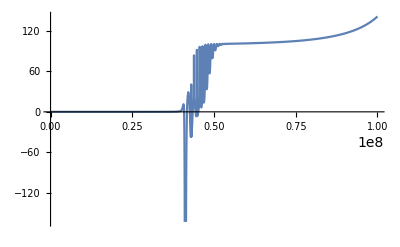

```mathematica
Plot[Evaluate[mss/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->Automatic]
```

```mathematica
Hfake=Sqrt[(1/2 velFake.Gfake.velFake+V/.{σ->σFake,θ->θFake})/3];
```

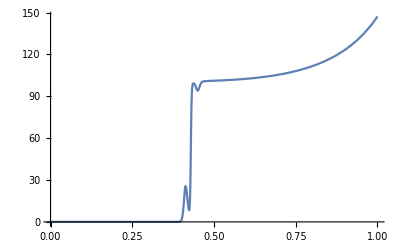

```mathematica
Plot[Evaluate[mssFake/Hfake^2/.{tEndTemp->1*^8,Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}],{t,0,1*^8},PlotRange->Automatic]
```